```mathematica
func= Plot[{x^2 + 1,(x-2)(x-4)},{x,-1,5},PlotLabels->{ToExpression["f_0",TeXForm],ToExpression["f_1",TeXForm]}];
feas=RegionPlot[(x-2)(x-4)<=0,{x,1,5},{y,-30,30},BoundaryStyle->{LightRed,Dashed},PlotStyle->{Directive[Orange,Opacity[0.2]]}];
opti=Graphics[{PointSize[Large],Pink,Point[{2,5}]}];
text=Graphics[{Text["Optimal",{2,4},{Center,Top}],Text["Feasible Set",{3,25}]}];
line=Graphics[{Dashed,Brown,Line[{{0,5},{2,5},{2,0}}]}];
Show[func,feas,opti,text,line]
```

-Graphics-

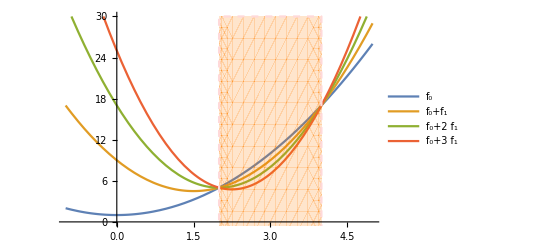

```mathematica
feas=RegionPlot[(x-2)(x-4)<=0,{x,1,5},{y,-30,30},BoundaryStyle->{LightRed,Dashed},PlotStyle->{Directive[Orange,Opacity[0.2]]}];
lagr=Plot[Evaluate[Table[(1+l)x^2-6 l x+1+8 l,{l,0,3}]],{x,-1,5},PlotRange->{0,30},PlotLegends->{ToExpression["f_0",TeXForm],ToExpression["f_0+f_1",TeXForm],ToExpression["f_0+2f_1",TeXForm],ToExpression["f_0+3f_1",TeXForm]}];
Show[lagr,feas]
```

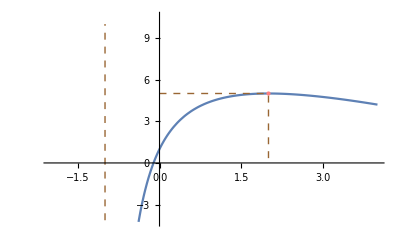

```mathematica
func = Plot[-9*l^2/(1+l)+1+8 l,{l,-2,4}];
line=Graphics[{Dashed,Brown,Line[{{-1,-10},{-1,10}}]}];
opti=Graphics[{PointSize[Large],Pink,Point[{2,5}]}];
dsline=Graphics[{Dashed,Brown,Line[{{0,5},{2,5},{2,0}}]}];
Show[func,line,opti,dsline]3
```

```mathematica
func=Graphics[Table[{Dashed,Circle[{0,0},Sqrt[r]]},{r,0.5,3,0.5}]];
fea1=RegionPlot[(x-1)^2+(y-1)^2<=1,{x,-2,2},{y,-2,2},BoundaryStyle->{LightRed,Dashed},PlotStyle->{Directive[Gray,Opacity[0.2]]},PlotLabels->ToExpression["f_1(x)\le0",TeXForm]];
fea2=RegionPlot[(x-1)^2+(y+1)^2<=1,{x,-2,2},{y,-2,2},BoundaryStyle->{LightRed,Dashed},PlotStyle->{Directive[Gray,Opacity[0.2]]},PlotLabels->ToExpression["f_2(x)\le0",TeXForm]];
opti=Graphics[{PointSize[Large],Pink,Point[{1,0}]}];
Show[fea1,func,fea2,opti]
```

-Graphics-

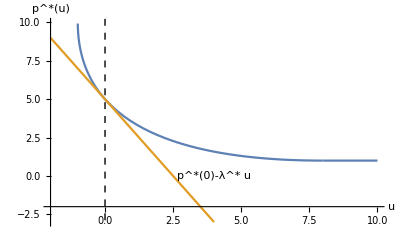

```mathematica
f[x_]=If[x>=8,1,11+x-6Sqrt[1+x]];
func = Plot[{f[x],f[0]+f'[0]x}, {x,-2,10},PlotRange->{-3,10},AxesLabel->{"u",ToExpression["p^*(u)",TeXForm]},AxesOrigin->{-2,-2}];
text = Text[ToExpression["p^*(0)-\lambda^*u",TeXForm],{4,0}];
line = Line[{{0,-10},{0,20}}];
Show[func,Graphics[text],Graphics[{Dashed, line}]]
```

```mathematica
f'
```

If[#1≥8,0,1-3/(√(1+#1))]&